```mathematica
M=5;
beta=0.1;
g=0.;
alpha=0.5;
l=0.9;
rz=0.5;
L=3;
epsilon=Exp[-2*L];
bVal=1-2*epsilon;

xi[z_,Delta_,OmegaA_,sign_]=M*(sign*Delta*z+OmegaA)

betaA=alpha+beta-1-xi^2

betaZ=Together[beta+2*alpha+2*alpha^2*(xi^4+2*g*xi^3+2*g^2*xi^2-5*xi^2-6*g*xi+3)/((xi^2-1)*(xi^4-6*xi^2-4*g*xi+3))]

nBetaZ=Numerator[betaZ]

dBetaZ=Denominator[betaZ]

q[z_,Delta_,OmegaA_]=((1-l)*nBetaZ+l*betaA*dBetaZ)/nBetaZ
F[z_,Delta_,OmegaA_]=(Sqrt[-q[z,Delta,OmegaA]/. xi->xi[z,Delta,OmegaA,1]]+Sqrt[-q[z,Delta,OmegaA]/. xi->xi[z,Delta,OmegaA,-1]])/(-z^2+1)
```

5 (OmegaA+Delta sign z)

-0.4-xi^2

(1.1 (-1.63636+6.72727 xi^2-6.54545 xi^4+1. xi^6))/((-1.+xi^2) (3.-6. xi^2+xi^4))

1.1 (-1.63636+6.72727 xi^2-6.54545 xi^4+1. xi^6)

(-1.+xi^2) (3.-6. xi^2+xi^4)

(0.909091 (0.9 (-0.4-xi^2) (-1.+xi^2) (3.-6. xi^2+xi^4)+0.11 (-1.63636+6.72727 xi^2-6.54545 xi^4+1. xi^6)))/(-1.63636+6.72727 xi^2-6.54545 xi^4+1. xi^6)

1/(1-z^2)(0.953463 √(-((0.9 (-0.4-25 (OmegaA-Delta z)^2) (-1.+25 (OmegaA-Delta z)^2) (3.-150. (OmegaA-Delta z)^2+625 (OmegaA-Delta z)^4)+0.11 (-1.63636+168.182 (OmegaA-Delta z)^2-4090.91 (OmegaA-Delta z)^4+15625. (OmegaA-Delta z)^6))/(-1.63636+168.182 (OmegaA-Delta z)^2-4090.91 (OmegaA-Delta z)^4+15625. (OmegaA-Delta z)^6)))+0.953463 √(-((0.9 (-0.4-25 (OmegaA+Delta z)^2) (-1.+25 (OmegaA+Delta z)^2) (3.-150. (OmegaA+Delta z)^2+625 (OmegaA+Delta z)^4)+0.11 (-1.63636+168.182 (OmegaA+Delta z)^2-4090.91 (OmegaA+Delta z)^4+15625. (OmegaA+Delta z)^6))/(-1.63636+168.182 (OmegaA+Delta z)^2-4090.91 (OmegaA+Delta z)^4+15625. (OmegaA+Delta z)^6))))

```mathematica
deltaValues=Range[0,1,0.01];
initialOmega=0. +0.0740584987723142 I;  (*Initial guess for the first Delta*)
rValues=Range[0,10,0.5]
omegaValues=Table[Table[initialOmega=OmegaA/. FindRoot[NIntegrate[F[z,Delta,OmegaA],{z,0,bVal}]==r,{OmegaA,initialOmega}],{Delta,deltaValues}],{r,rValues}]
(*Assuming omegaValues,deltaValues,and rValues are already defined*)(*Flatten omegaValues and repeat deltaValues and rValues to match the length*)flatOmegaValues=Flatten[omegaValues];
repeatedDeltaValues=Flatten[Table[deltaValues,{Length[rValues]}]];
repeatedRValues=Flatten[Table[ConstantArray[r,Length[deltaValues]],{r,rValues}]];

(*Create the table*)
table=Transpose[{repeatedRValues,repeatedDeltaValues,flatOmegaValues}];

(*Convert the table to a Dataset for better visualization*)
dataset=Dataset[AssociationThread[{"rValues","deltaValues","omegaValues"}->#]&/@table]
```

{0.,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,9.5,10.}

NIntegrate::inumr: The integrand (1.90693 √(-(0.9 (-0.4-25 Power[«2»]) (-1.+25 Power[«2»]) (3.-150. Power[«2»]+625 Power[«2»])+0.11 («1»))/(-1.63636+168.182 Plus[«2»]^2-4090.91 Plus[«1»]^4+15625. Plus[«2»]^6)))/(1-z^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,0.995042}}.

NIntegrate::inumr: The integrand (0.953463 (-(0.9 (-0.4-25 Power[«2»]) (-1.+25 Power[«2»]) (-300. Plus[«2»]+2500 Power[«2»])+«1»-«1»+0.11 («1»))/(-1.63636+168.182 Plus[«2»]^2-4090.91 Plus[«1»]^4+15625. Plus[«2»]^6)+((«1») «1»)/(«1»)^2))/(√(-(0.9 (-0.4-25 Power[«2»]) (-1.+25 Power[«2»]) (3.-150. Power[«2»]+625 Power[«2»])+0.11 («1»))/(-1.63636+168.182 Plus[«2»]^2-4090.91 Plus[«2»]^4+15625. Plus[«2»]^6)) (1-z^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,0.995042}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {0.359521}. NIntegrate obtained 10.401+0. ⅈ and 0.0000940943 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {0.907572}. NIntegrate obtained 10.4018+0. ⅈ and 0.0000155496 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {0.359521}. NIntegrate obtained 10.3984+0. ⅈ and 0.0106244 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

Dataset[<>]

```mathematica
Normal[dataset]
```

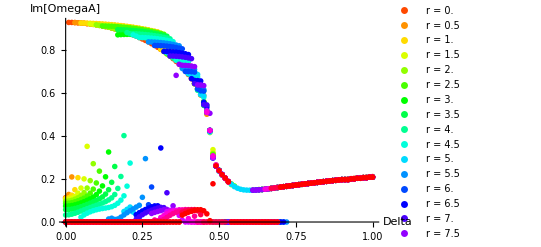

```mathematica
(*Assuming omegaValues,deltaValues,and rValues are already defined*)(*Create a list of data for each r value*)data=Table[Transpose[{deltaValues,Abs[Im[omegaValues[[i]]]]}],{i,Length[rValues]}];

(*Create a list of plot styles for each r value*)
plotStyles=Table[{Hue[i/Length[rValues]],PointSize[0.01]},{i,Length[rValues]}];

(*Create the plot*)
ListPlot[data,PlotStyle->plotStyles,Joined->False,PlotRange->All,AxesLabel->{"Delta","Im[OmegaA]"},PlotLegends->(StringJoin["r = ",ToString[#]]&/@rValues)]
```

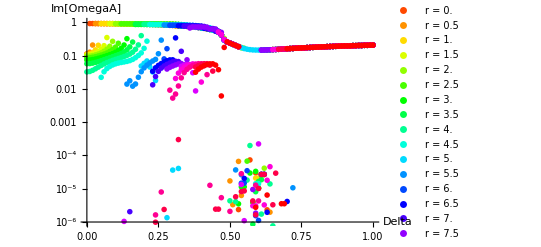

```mathematica
(*Assuming omegaValues,deltaValues,and rValues are already defined*)(*Create a list of data for each r value*)data=Table[Transpose[{deltaValues,Abs[Im[omegaValues[[i]]]]}],{i,Length[rValues]}];

(*Create a list of plot styles for each r value*)
plotStyles=Table[{Hue[i/Length[rValues]],PointSize[0.01]},{i,Length[rValues]}];

(*Create the plot*)
ListLogPlot[data,PlotStyle->plotStyles,Joined->False,PlotRange->{All,{10^-6,1}},(*Set the y-axis range from 10^-6 to 1*)AxesLabel->{"Delta","Im[OmegaA]"},PlotLegends->(StringJoin["r = ",ToString[#]]&/@rValues)]
```

```mathematica
(*Assuming omegaValues,deltaValues,and rValues are already defined*)(*Create a list of data for each r value*)data=Table[Transpose[{deltaValues,Abs[Im[omegaValues[[i]]]]}],{i,Length[rValues]}];

(*Create a list of plot styles for each r value*)
plotStyles=Table[{Hue[i/Length[rValues]],PointSize[0.01]},{i,Length[rValues]}];

(*Create the interactive plot*)
Manipulate[ListPlot[data[[i]],PlotStyle->plotStyles[[i]],Joined->False,PlotRange->All,AxesLabel->{"Delta","Im[OmegaA]"},PlotLabel->StringJoin["r = ",ToString[rValues[[i]]]]],{{i,1,"r value"},1,Length[rValues],1}]
```

```mathematica
(*Assuming omegaValues,deltaValues,and rValues are already defined*)(*Create a list of data for each r value*)data=Table[Transpose[{deltaValues,Abs[Im[omegaValues[[i]]]]}],{i,Length[rValues]}];

(*Create a list of plot styles for each r value*)
plotStyles=Table[{Hue[i/Length[rValues]],PointSize[0.01]},{i,Length[rValues]}];

(*Create a list of plots for each r value*)
plots=Table[ListPlot[data[[i]],PlotStyle->plotStyles[[i]],Joined->False,PlotRange->{0,1},AxesLabel->{"Delta","Im[OmegaA]"},PlotLabel->StringJoin["r = ",ToString[rValues[[i]]]]],{i,Length[rValues]}];

(*Export the animation as a GIF*)
Export["animation.gif",plots,"DisplayDurations"->0.3]
```

animation.gif